```mathematica
(*define model*)
QS=F[S,ρN/β];
QR=F[ρC,R];
(*full set of fluxes, in form {flux name, formula}*)
tsolve=tsolve={
{ρN,R-QR},
{ρC,S-QS}
};
(*labels for fluxes: for plotting*)
names={ρN->"ρ_N",ρC->"ρ_C"};
(*get the adjacency matrix*)
matrix=Table[FreeQ[row[[2]],x],{row,tsolve},{x,tsolve[[All,1]]}]/.{True->0,False->1};
(*show the matrix*)
TableForm[matrix,TableHeadings->{#,#}&@(tsolve[[All,1]]/.names)]
```

| ρ_N | ρ_C
ρ_N | 0 | 1
ρ_C | 1 | 0

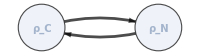

```mathematica
(*pairs of position in adjacency matrix and corresponding flux*)
numbers=Transpose[{Range@Length@#,#}]&@tsolve[[All,1]];
(*replacement rule to replace positions in adjacency matrix with flux names*)
fluxtonumber=#[[2]]->#[[1]]&/@numbers;
(*make a graph from the fluxes in tsolve (using the adjency matrix), for later: mark all markeds yellow*)graph[matrix_,markeds_]:=AdjacencyGraph[matrix,VertexStyle->Table[i->Piecewise[{{Yellow, MemberQ[markeds/.fluxtonumber,i]}, {Lighter[ColorData[97][1],.9], True}}],
{i,Length@tsolve}],VertexSize->{{.2,.2}},VertexLabels->(#[[1]]->Placed[#[[2]],Center]&/@numbers/.names),VertexLabelStyle->Directive[10,Bold,Italic],ImageSize->200,EdgeStyle->{{Thickness[Scaled[.01]],Black}},GraphLayout->"SpringElectricalEmbedding",DirectedEdges->True];
graph[matrix,{}]
```

```mathematica
(*adjacency matrix when fluxes at the positions columns are bufferd: set columns to 0*)
reducematrix[columns_]:=ReplacePart[matrix,Table[{i_,column}->0,{column,columns}]];
(*test if graph is acyclic (and in Mathematica terms has has no self loops)*)
GoodGraphQ:=AcyclicGraphQ[#]∧LoopFreeGraphQ[#]&;
(*get all possible flux combinations up to level*)
acycliccombinations[level_]:=Subsets[tsolve[[All,1]],level];
(*find all combinations with a given number of fluxes as state variables (maximally maxlevel) that make the graph having no cycles. Exclude redundant solutions (that just add state variables to lower level solutions)*)
maxlevel=2;
Clear[fluxsolutions];
Table[fluxsolutions[level]=Table[If[GoodGraphQ[graph[reducematrix[statefluxes/.fluxtonumber],{}]],statefluxes,Nothing],{statefluxes,Select[acycliccombinations[{level}],If[level==0,True,And@@Table[Not@SubsetQ[#,lowersolution],{lowersolution,Flatten[Table[fluxsolutions[lowerlevel],{lowerlevel,0,level-1}],1]}]]&]}],{level,0,maxlevel}];
```

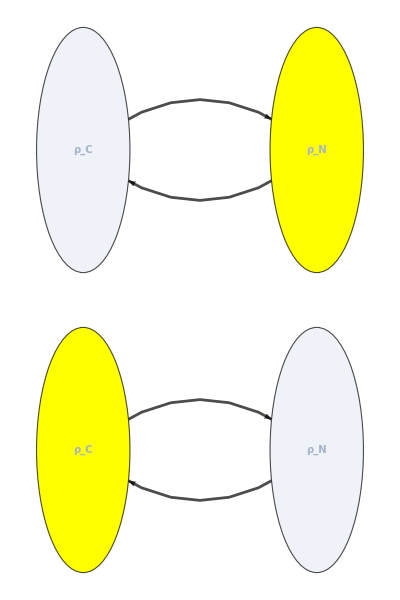
Root-shoot model. Cycle-free versions of graph for the auxiliary variables. Yellow: auxiliary variables that when buffered interrupt all cycles in the graph.
Do not show redundant solutions (that just add buffers to ready solutions with less buffers).
--------------
Number of buffers: 0

--------------
Number of buffers: 1
-Graphics-
--------------
Number of buffers: 2

```mathematica
(Export[NotebookDirectory[]<>"fluxplots-root-shoot.pdf",#];#)&@Column[Join[{TextCell["Root-shoot model. Cycle-free versions of graph for the auxiliary variables. Yellow: auxiliary variables that when buffered interrupt all cycles in the graph.\nDo not show redundant solutions (that just add buffers to ready solutions with less buffers)."]},Table[
Column[{"--------------",Row[{"Number of buffers: ",level}],
Column[Table[graph[matrix,statefluxes],{statefluxes,fluxsolutions[level]}]]}],
{level,0,maxlevel}]]]
```